# Bunimovich

## 1. Inicialización y Generación de la Geometría

Primero, cargamos la librería y definimos la rejilla del estadio. El estadio de Bunimovich es un sistema caótico icónico compuesto por un rectángulo y dos tapas semicirculares.

Sitios espaciales: 3097

Dimension total del sistema (4 estados): 12388

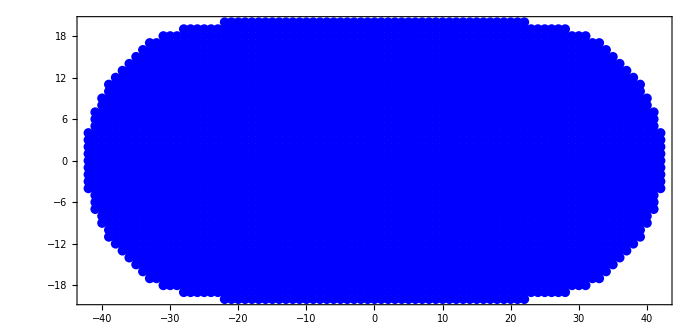

```mathematica
(* Cargar la libreria *)
Needs/@{"QuantumWalks`","QMB`"};

(* Parametros del estadio *)
Semilongitud = 22; (* L *)
Radio = 20;         (* R *)

(* Generar la rejilla completa *)
GridEstadio = GenerateFullStadiumBasis[Semilongitud, Radio];

Print["Sitios espaciales: ", GridEstadio["Dimension"]];
Print["Dimension total del sistema (4 estados): ", 4 * GridEstadio["Dimension"]];

(* Visualizacion *)
ListPlot[GridEstadio["Coords"], AspectRatio -> Automatic, 
  PlotStyle -> {PointSize[0.01], Blue}, Frame -> True, 
ImageSize->700,LabelStyle->Directive[Black,22]]
```

## 2. Construcción del Operador de Evolución (U)

Para estudiar las propiedades espectrales, necesitamos el operador unitario U=S⋅C. Utilizaremos una moneda de Grover, que es la que mejor resalta las propiedades de caos cuántico.

```mathematica
(* 1. Operador de Desplazamiento (Shift) para 4 estados *)
OperadorS = BuildShiftOperators[GridEstadio, CoinDimension -> 4];

(* 2. Operador Moneda (Coin) - Grover *)
DimEspacial = GridEstadio["Dimension"];
MatrizGrover = ConstantArray[1/2., {4, 4}] - IdentityMatrix[4];
OperadorC = KroneckerProduct[
  IdentityMatrix[DimEspacial, SparseArray], 
  SparseArray[MatrizGrover]
];

(* 3. Evolucion total *)
OperadorUTotal = OperadorS . OperadorC;
```

## 3. Construcción de Isometrías de Simetría

El estadio tiene simetría $C_{2v}$. Usamos BuildSymmetryIsometry para obtener las matrices $V$ que proyectan el sistema en sus 4 sectores independientes: $A_1$, $A_2$, $B_1$, y $B_2$.

```mathematica
(* Definimos las etiquetas de los sectores *)
Etiquetas = {"A1", "A2", "B1", "B2"};

(* Construimos las isometrias (Matrices V) *)
MatricesV = Map[BuildSymmetryIsometry[GridEstadio, #] &, Etiquetas];

(* Verificamos dimensiones de los subespacios *)
DimensionesSectores = Map[Last[Dimensions[#]] &, MatricesV];

TableForm[Transpose[{Etiquetas, DimensionesSectores}], 
  TableHeadings -> {None, {"Sector", "Dimension"}}]
```

Sector | Dimension
A1 | 3160
A2 | 3034
B1 | 3075
B2 | 3119

## 4. Proyección y Análisis Espectral

Ahora proyectamos $U$ en cada sector. Esto reduce drásticamente el costo computacional. Por ejemplo, si el sistema total es de dimensión 4000, cada sector tendrá $\approx 1000$. Calcularemos las cuasi-energías (fases de los autovalores).

```mathematica
(* Proyectamos el operador en cada sector *)
OperadoresReducidos = Map[
  Chop[ConjugateTranspose[#] . OperadorUTotal . #] &, 
  MatricesV
];

(* Extraemos autovalores de un sector especifico (ej. A1) *)
AutovaloresA1 = Eigenvalues[Normal[OperadoresReducidos[[1]]]];

(* Las cuasi-energias son las fases de los autovalores unitarios *)
CuasiEnergiasA1 = Sort[Arg[AutovaloresA1]];
```

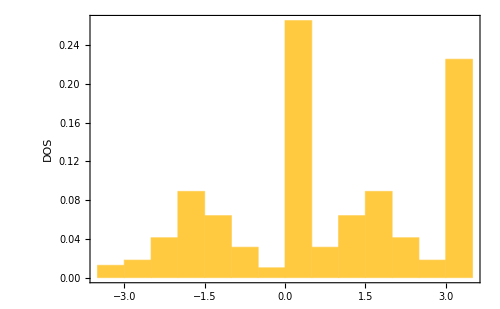

```mathematica
(* DOS *)
Histogram[CuasiEnergiasA1, Automatic, "Probability", 
  Frame -> True, FrameLabel -> {"", "DOS"},FrameStyle->Directive[Black,20],
ImageSize->500]
```

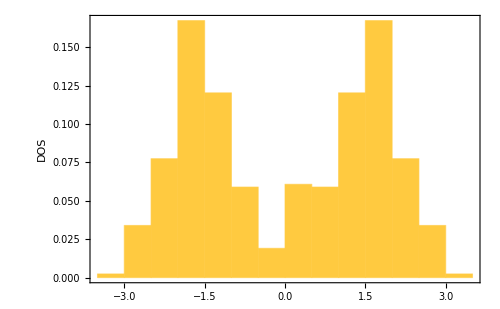

```mathematica
(* DOS filtrando ϕ=-π,0,π *)
CuasiEnergiasA1Filtradas=Select[CuasiEnergiasA1,0.<#<Pi||-Pi<#<0.&];
Histogram[CuasiEnergiasA1Filtradas, Automatic, "Probability", 
  Frame -> True, FrameLabel -> {"", "DOS"},FrameStyle->Directive[Black,20],
ImageSize->500]
```

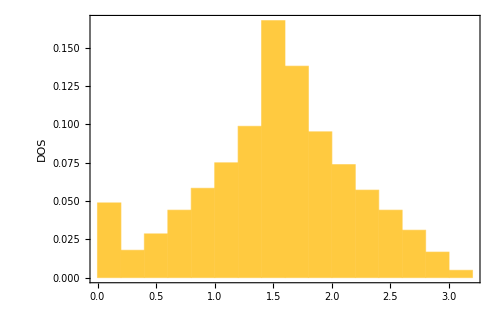

```mathematica
Histogram[Select[CuasiEnergiasA1Filtradas,#>0&], Automatic, "Probability", 
  Frame -> True, FrameLabel -> {"", "DOS"},FrameStyle->Directive[Black,20],
ImageSize->500]
```

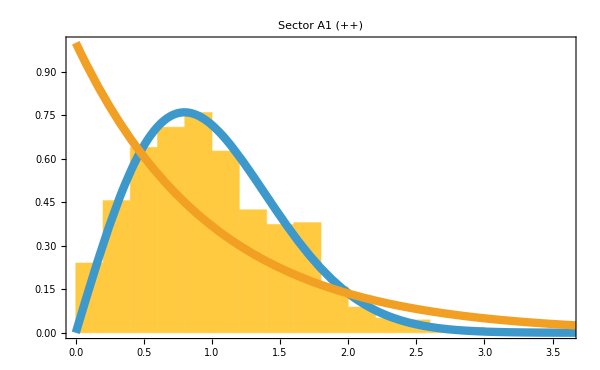

```mathematica
(* Espacimiento de niveles *)
CuasiEnergiasA1Filtradas2=Select[CuasiEnergiasA1Filtradas,#>0&];
Espaciamientos = Differences[Unfold[CuasiEnergiasA1Filtradas2]["UnfoldedLevels"][[50;;]]];

Show[
Histogram[Espaciamientos, Automatic, "PDF", 
  PlotLabel -> "Sector A1 (++)",
LabelStyle->Directive[Black,20],
  Frame -> True, FrameStyle->Directive[Black,24],
FrameLabel->{"", ""},ImageSize->600],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,4},PlotStyle->Thickness[0.01]]
]
```

## 5. Verificación de la Isometría

Es vital que tu colega entienda que $V$ debe ser una isometría perfecta ($V^\dagger V = \mathbb{I}$). Podemos verificarlo visualmente para asegurar que no hay pérdida de probabilidad.

```mathematica
(* Verificar que V es isometrica para el primer sector *)
V = MatricesV[[1]];
IdentidadCheck = Chop[ConjugateTranspose[V] . V];

(* Deberia ser una matriz identidad de la dimension del sector *)
Print["¿V es isometrica? ", 
  IdentidadCheck == IdentityMatrix[Last[Dimensions[V]], SparseArray]];
```

¿V es isometrica? True

# Billar de Sinaí (simetría $C_{4v}$)

Este sistema es un cuadrado con un obstáculo circular en el centro. Para evitar la degeneración de los estados dobles (representación $E$), proyectaremos el operador en los 6 sectores puros ($A_1, A_2, B_1, B_2, E_x, E_y$) que garantizan unitariedad y limpieza espectral.

## A . Inicialización y Geometría

Cargamos los parámetros y visualizamos la red . Nota que el semi - lado $L$ define un cuadrado total de $2L\times 2 L$

Dimensión espacial: 5864

Dimensión total (4 estados): 23456

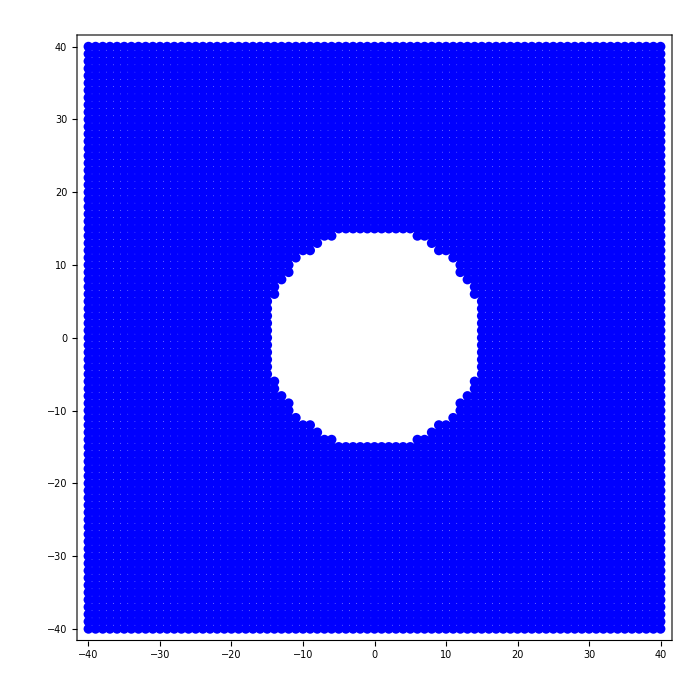

```mathematica
(*Cargar librerías y configurar parámetros*)Needs["QuantumWalks`"];
Semilado=40; (*L*)
Radio=15;     (*R*)

(*Generar rejilla completa del Sinai*)
GridSinai=GenerateFullSinaiBasis[Semilado,Radio];
DimEspacial=GridSinai["Dimension"];

Print["Dimensión espacial: ",DimEspacial];
Print["Dimensión total (4 estados): ",4*DimEspacial];

(*Visualización*)
ListPlot[GridSinai["Coords"],AspectRatio -> Automatic, 
  PlotStyle -> {PointSize[0.01], Blue}, Frame -> True, 
ImageSize->700,LabelStyle->Directive[Black,22]]
```

## B . Dinámica y Proyección Espectral

Aquí construimos el operador de evolución de 4 estados y lo proyectamos usando las 6 isometrías desimetrizadas.

```mathematica
(* 1. Operador de Evolución Global *)
OperadorS = BuildShiftOperators[GridSinai, CoinDimension -> 4];
MatrizGrover = ConstantArray[1/2., {4, 4}] - IdentityMatrix[4];
OperadorC = KroneckerProduct[IdentityMatrix[DimEspacial, SparseArray], 
  SparseArray[MatrizGrover]];
OperadorUTotal = OperadorS . OperadorC;

(* 2. Construcción de Isometrías (C4v Sectors) *)
Sectores = {"C4v_A1", "C4v_A2", "C4v_B1", "C4v_B2", "C4v_Ex", "C4v_Ey"};
Isometrias = Map[BuildSymmetryIsometry[GridSinai, #] &, Sectores];

(* 3. Proyección y Cálculo de Dimensiones *)
OperadoresU = Map[Chop[ConjugateTranspose[#] . OperadorUTotal . #] &, Isometrias];
Dimensiones = Map[Last[Dimensions[#]] &, Isometrias];

(* Reporte de completitud *)
Print["Suma de dimensiones: ", Total[Dimensiones]];
Print["¿Completo? ", Total[Dimensiones] == 4 * DimEspacial];
```

Suma de dimensiones: 3584

¿Completo? True

# Cardioide

El cardioide rompe la simetría en el eje $X$ pero mantiene la reflexión en $Y$ . Por lo tanto, solo existen dos sectores : Even (Par) y Odd (Impar) .

## 1. Geometría

El cardioide se define algebraicamente y se extiende principalmente en los valores negativos de $X$.

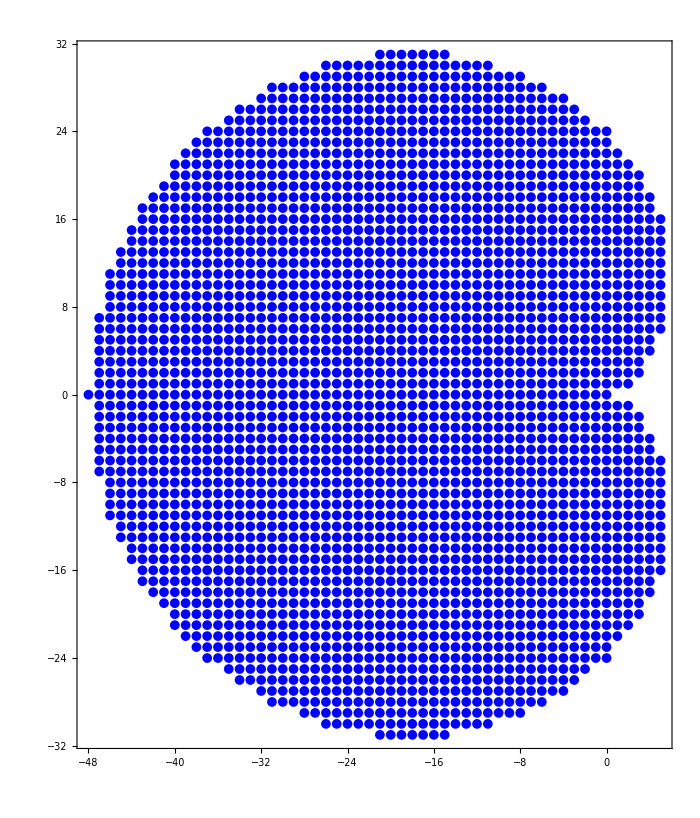

```mathematica
(* Parámetro de escala *)
RadioCardioide = 12;

(* Generar rejilla del cardioide *)
GridCardioide = GenerateCardioidBasis[RadioCardioide];
DimCardioide = GridCardioide["Dimension"];

(* Visualización de la asimetría horizontal *)
ListPlot[GridCardioide["Coords"], AspectRatio -> Automatic, 
  PlotStyle -> {PointSize[0.01], Blue}, Frame -> True, 
ImageSize->700,LabelStyle->Directive[Black,22]]
```

## 2. Isometrías de Paridad y Unitaridad

En este caso, BuildSymmetryIsometry detecta automáticamente que se trata de simetría bilateral al recibir las etiquetas “Even” u “Odd”.

```mathematica
(* 1. Operador U para el Cardioide *)
OpSCardioide = BuildShiftOperators[GridCardioide, CoinDimension -> 4];
OpCCardioide = KroneckerProduct[IdentityMatrix[DimCardioide, SparseArray], 
  SparseArray[MatrizGrover]];
UCardioide = OpSCardioide . OpCCardioide;

(* 2. Proyección en los 2 sectores de paridad *)
SectoresBilat = {"Even", "Odd"};
IsometriasCardioide = Map[BuildSymmetryIsometry[GridCardioide, #] &, SectoresBilat];

(* 3. Operadores Reducidos *)
UReducidosCardioide = Map[
  Chop[ConjugateTranspose[#] . UCardioide . #] &, 
  IsometriasCardioide
];

(* Verificación de Unitaridad *)
MapThread[
  Print["Sector: ", #1, " | Unitaria: ", UnitaryMatrixQ[#2]] &, 
  {SectoresBilat, UReducidosCardioide}
];
```

Sector: Even | Unitaria: True

Sector: Odd | Unitaria: True